```mathematica
ClearAll["Global`*"]
```

```mathematica
(* given rational (r,s=d) in A^2, returns (m,y) that is a solution to S *)
ϕ[r_,s_]:={(-4-4 r-r^2-4 s^2-2 r s^2+s^4)/(8 r),(-4+r^2-4 s^2+s^4)/(2 r)};
(* given m and d, return gamma *)
gamma[m_,d_]:=Sign[d] Sqrt[2 d^4+8m d^2+16 m^2+16m](-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)+17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m;
```

```mathematica
f[x_]:=(x-γ)^2+γ+m;
p1[x_]:=(x-γ)^4+d(x-γ)^3+c(x-γ)^2+b(x-γ)+a;
p2[x_]:=(x-γ)^4-d(x-γ)^3+c(x-γ)^2-b(x-γ)+a;
```

```mathematica
Collect[f[f[f[x]]],x-γ]
```

m+m^2+2 m^3+m^4+(4 m^2+4 m^3) (x-γ)^2+(2 m+6 m^2) (x-γ)^4+4 m (x-γ)^6+(x-γ)^8+γ

```mathematica
Collect[p1[x]p2[x],x-γ]
```

a^2+(-b^2+2 a c) (x-γ)^2+(2 a+c^2-2 b d) (x-γ)^4+(2 c-d^2) (x-γ)^6+(x-γ)^8

```mathematica
Clear[m,γ]
```

```mathematica
sys={m+m^2+2 m^3+m^4+γ==a^2,
4 m^2+4 m^3==-b^2+2 a c,
2 m+6 m^2==2 a+c^2-2 b d,
4 m==2 c-d^2};
sys//TableForm
```

m+m^2+2 m^3+m^4+γ==a^2
4 m^2+4 m^3==-b^2+2 a c
2 m+6 m^2==2 a+c^2-2 b d
4 m==2 c-d^2

```mathematica
Clear[a,b,c,d];
Solve[sys,{a,b,c,γ}][[1,4]]
```

γ→1/64 (17 d^8-64 m+112 d^4 m+80 d^6 m+128 d^2 m^2+176 d^4 m^2+128 d^2 m^3-12 √2 d^4 √(d^4 (d^4+8 m+4 d^2 m+8 m^2))-32 √2 m √(d^4 (d^4+8 m+4 d^2 m+8 m^2))-32 √2 d^2 m √(d^4 (d^4+8 m+4 d^2 m+8 m^2))-32 √2 m^2 √(d^4 (d^4+8 m+4 d^2 m+8 m^2)))

```mathematica
Solve[y^2==2(d^4+4 d^2 m+8 m (1+m)),m]
```

{{m→1/4 (-2-d^2-√(4+4 d^2-d^4+y^2))},{m→1/4 (-2-d^2+√(4+4 d^2-d^4+y^2))}}

```mathematica
Show[
ContourPlot[{(-2 d^2-d^4-√(4 d^4+4 d^6-d^8+d^2 y^2))/(4 d^2)},{d,-5,5},{y,-10,10},ContourShading->False,Contours->100,MaxRecursion->3],
ContourPlot[{(-2 d^2-d^4+√(4 d^4+4 d^6-d^8+d^2 y^2))/(4 d^2)},{d,-5,5},{y,-10,10},ContourShading->False,Contours->100,MaxRecursion->3]
]
```

-Graphics-

```mathematica
gamma[ϕ[r,s][[1]],s]
```

(17 s^8)/64-(-4-4 r-r^2-4 s^2-2 r s^2+s^4)/(8 r)+(7 s^4 (-4-4 r-r^2-4 s^2-2 r s^2+s^4))/(32 r)+(5 s^6 (-4-4 r-r^2-4 s^2-2 r s^2+s^4))/(32 r)+(s^2 (-4-4 r-r^2-4 s^2-2 r s^2+s^4)^2)/(32 r^2)+(11 s^4 (-4-4 r-r^2-4 s^2-2 r s^2+s^4)^2)/(256 r^2)+(s^2 (-4-4 r-r^2-4 s^2-2 r s^2+s^4)^3)/(256 r^3)+√(2 s^4+(2 (-4-4 r-r^2-4 s^2-2 r s^2+s^4))/r+(s^2 (-4-4 r-r^2-4 s^2-2 r s^2+s^4))/r+((-4-4 r-r^2-4 s^2-2 r s^2+s^4)^2)/(4 r^2)) (-(3 s^6)/16-(s^2 (-4-4 r-r^2-4 s^2-2 r s^2+s^4))/(16 r)-(s^4 (-4-4 r-r^2-4 s^2-2 r s^2+s^4))/(16 r)-(s^2 (-4-4 r-r^2-4 s^2-2 r s^2+s^4)^2)/(128 r^2))

```mathematica
(* this is m *)
(-4-4 r-r^2-4 s^2-2 r s^2+s^4)/(8 r)
```

```mathematica
gamma[m,s]
```

-m+2 m^2 s^2+2 m^3 s^2+(7 m s^4)/4+(11 m^2 s^4)/4+(5 m s^6)/4+(17 s^8)/64+√(16 m+16 m^2+8 m s^2+2 s^4) (-(m s^2)/2-(m^2 s^2)/2-(m s^4)/2-(3 s^6)/16)

```mathematica
gamma[-1,s]//FullSimplify
```

1+s^4-(5 s^6)/4+(17 s^8)/64+√(-8 s^2+2 s^4) (s^4/2-(3 s^6)/16)

```mathematica
With[{m=M/Z,a=A/Z,b=B/Z,c=CC/Z,d=DD/Z,γ=GAMMA/Z},
Print[{Z^4*(m+m^2+2 m^3+m^4+γ-a^2),
Z^3*(4 m^2+4 m^3-(-b^2+2 a c)),
Z^2*(2 m+6 m^2-(2 a+c^2-2 b d)),
Z^2*(4 m-(2 c-d^2))}//Expand//InputForm];
]
```

{M^4 + 2*M^3*Z - A^2*Z^2 + M^2*Z^2 + GAMMA*Z^3 + M*Z^3, 4*M^3 + B^2*Z - 2*A*CC*Z + 4*M^2*Z, -CC^2 + 2*B*DD + 6*M^2 - 2*A*Z + 2*M*Z, DD^2 - 2*CC*Z + 4*M*Z}

```mathematica
d^6+4 d^4 m+8 d^2 m (1+m)-y^2//Expand//InputForm
```

d^6 + 8*d^2*m + 4*d^4*m + 8*d^2*m^2 - y^2

```mathematica
With[{d=R^3*S-3*R^2*S^2+5*R*S^3-3*S^4+R^2*S*Z-3*R*S^2*Z+2*S^3*Z,
y=R^4-4*R^3*S+6*R^2*S^2-4*R*S^3+S^4+R^3*Z-4*R^2*S*Z+7*R*S^2*Z-6*S^3*Z+1/2*R^2*Z^2-2*R*S*Z^2+2*S^2*Z^2,
m=-1/4*R^4+R^3*S-3/2*R^2*S^2+R*S^3-1/4*S^4+1/8*R^2*Z^2-1/2*R*S*Z^2+1/2*S^2*Z^2,
z=R^2*S^2-2*R*S^3+3*S^4+R*S^2*Z-2*S^3*Z},
FullSimplify[2(d^4+4 d^2 m z+8 m (1 z^3+m z^2))-y^2 z^2]
]
```

0

```mathematica
(*   returns {d, y, m, z}   *)
toProjectiveS[r_,s_]:=Module[{den,Z,R,S},
den=Denominator/@{r,s};
Z=LCM[den[[1]],den[[2]]];
R=r*Z;
S=s*Z;
Return[{R^3*S-3*R^2*S^2+5*R*S^3-3*S^4+R^2*S*Z-3*R*S^2*Z+2*S^3*Z,
R^4-4*R^3*S+6*R^2*S^2-4*R*S^3+S^4+R^3*Z-4*R^2*S*Z+7*R*S^2*Z-6*S^3*Z+1/2*R^2*Z^2-2*R*S*Z^2+2*S^2*Z^2,
-1/4*R^4+R^3*S-3/2*R^2*S^2+R*S^3-1/4*S^4+1/8*R^2*Z^2-1/2*R*S*Z^2+1/2*S^2*Z^2,
R^2*S^2-2*R*S^3+3*S^4+R*S^2*Z-2*S^3*Z}];
]
(*   returns {m, d, y}  *)
toS[r_,s_]:=Module[{d,y,m,z},
{d,y,m,z}=toProjectiveS[r,s];
Return[{m/z,d/z, y/z}];
]
```

```mathematica
{m,d}=toS[1,1];
{m,gamma[m,d]}
```

{1/8,-1/8}

```mathematica
With[{m=toS[-1,1][[1]],d=toS[-1,1][[2]]},
γ=gamma[m,d];
Print[{m,γ}];
f[x_]:=(x-γ)^2+m+γ;
Print[IrreduciblePolynomialQ/@{f[x],f[f[x]],f[f[f[x]]]}];
]
```

{-23/24,71/27}

{True,True,False}

```mathematica
Show[
ParametricPlot[{ϕ[r,s][[1]],gamma[ϕ[r,s][[1]],s]},{r,-1,10},{s,-1,10},PlotRange->{{-10,10},{-10,10}},PlotStyle->ColorData["DarkRainbow"]]
,
ParametricPlot[{toS[r,s][[1]],gamma[toS[r,s][[1]],toS[r,s][[2]]]},{r,-1,10},{s,-1,10},PlotRange->{{-10,10},{-10,10}}]

]
```

```mathematica
map1images={}; (* using map from Japanese prof *)
map2images={}; (* using map from Magma *)
Do[Do[
m=ϕ[r,s][[1]];
AppendTo[map1images,{m,gamma[m,s]}];
{m,d, y}=toS[r,s];
AppendTo[map2images,{m,gamma[m,d]}];
,{r,-10,10,1/10}],{s,-10,10,1/10}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 20000+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression -187500+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 96059601/5000+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ListPlot[{map1images,map2images},PlotRange->{{-10,2},{-40,60}},PlotStyle->{PointSize[.001],PointSize[.001]},ImageSize->1000]
```

```mathematica
commonPoints={};
Do[
If[Length[Position[map2images,im]]≠0,
AppendTo[commonPoints,im];
];
,{im,map1images}]
```

```mathematica
commonPoints//Length
```

390

```mathematica
Select[commonPoints,(#[[1]]<100000000000)&]//Length
```

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

189

```mathematica
Position[map1images,{-7/4,1/2}]
```

{}

```mathematica
m=ϕ[1,-1][[1]];
{m,gamma[m,-1]}
```

{-7/4,1/2}

```mathematica
{m,d}=toS[0,1/2];
γ=gamma[m,d];
{m,γ}//Simplify
f[x_]:=(x-γ)^2+γ+m;
IrreduciblePolynomialQ/@{f[x],f[f[x]],f[f[f[x]]]}
```

{-7/4,1/2}

{True,True,False}

```mathematica
gamma[m,0]
```

-m

```mathematica
gamma[m,0]
```

-m

```mathematica
Sign[0]
```

0

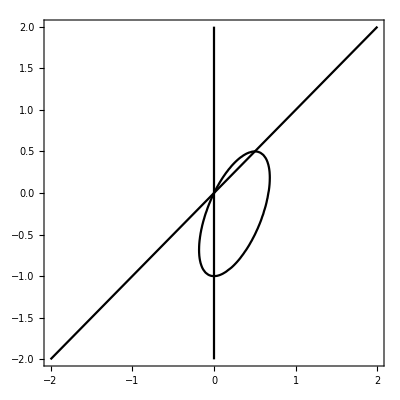

```mathematica
ContourPlot[{r^2-2r s+3s^2+r-2s==0,s==0,s==r},{s,-2,2},{r,-2,2},ContourStyle->{Black,Black}]
```

```mathematica
{m,y}=ϕ[r,s];
d=s;
γ=- y (-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)+17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m;
-m-γ//FullSimplify
m^2+m+γ//FullSimplify
```

-(s^2 (-4 (2+r)+(-8+r) s^2+2 s^4) (-4 (1+s^2)+(r+s^2)^2)^2)/(256 r^3)

((-2 (2+r)+(-4+r) s^2+s^4)^2 (r (2+r)^2+4 (-2+r+r^2) s^2+(-8+5 r) s^4+2 s^6))/(256 r^3)

```mathematica
-r(-4 (2+r)+(-8+r) s^2+2 s^4)//Expand

r(r (2+r)^2+4 (-2+r+r^2) s^2+(-8+5 r) s^4+2 s^6)//Expand
```

8 r+4 r^2+8 r s^2-r^2 s^2-2 r s^4

4 r^2+4 r^3+r^4-8 r s^2+4 r^2 s^2+4 r^3 s^2-8 r s^4+5 r^2 s^4+2 r s^6

```mathematica
With[{r=1,s=1},
Mod[4 r^2+4 r^3+r^4-8 r s^2+4 r^2 s^2+4 r^3 s^2-8 r s^4+5 r^2 s^4+2 r s^6,5]
]
```

3

```mathematica
n=5;
Mod[#^2,n]&/@Range[0,n-1]//TableForm
```

0
1
4
4
1

```mathematica
With[{r=5x,s=1},
Mod[4 r^2+4 r^3+r^4-8 r s^2+4 r^2 s^2+4 r^3 s^2-8 r s^4+5 r^2 s^4+2 r s^6,3]
]
```

Mod[-70 x+325 x^2+1000 x^3+625 x^4,3]

```mathematica
FullSimplify[-m-m^2-2 m^3-m^4+1/64 (3 d^4+8 d^2 m+8 m (1+m)-2 √2 d √(d^6+4 d^4 m+8 d^2 m (1+m)))^2 == (17 d^8)/64-m+(7 d^4 m)/4+(5 d^6 m)/4+2 d^2 m^2+(11 d^4 m^2)/4+2 d^2 m^3+√(2 d^4+16 m+8 d^2 m+16 m^2) (-(3 d^6)/16-(d^2 m)/2-(d^4 m)/2-(d^2 m^2)/2)  , {d>0}]
```

True

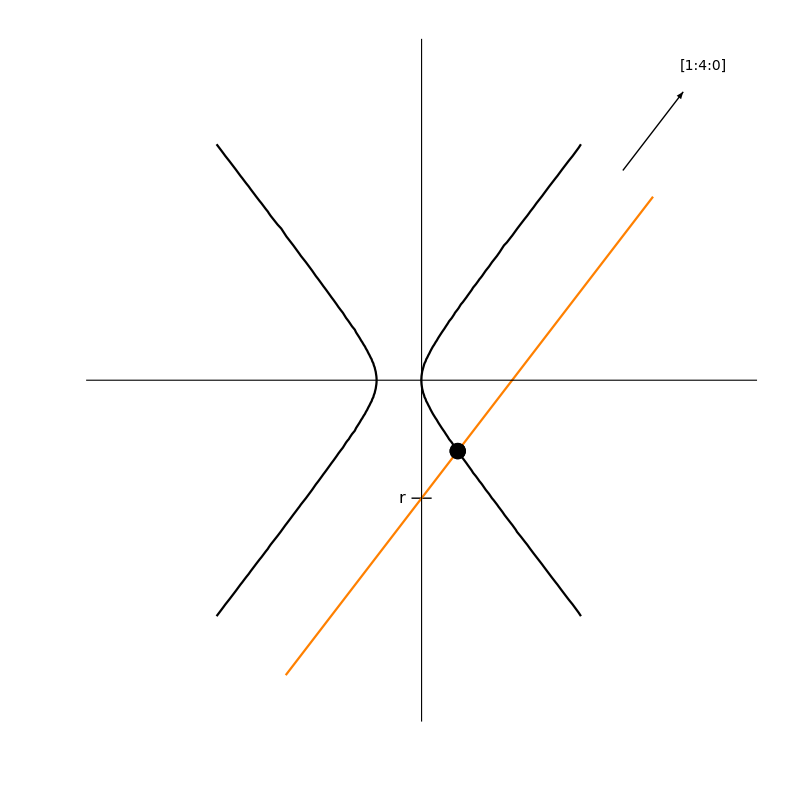

```mathematica
With[{s=-1/2},
Show[
ContourPlot[,{m,-8,8},{y,-25,25},AspectRatio->1,Axes->True,Ticks->None,Frame->False],
Graphics[Line[{{-1/4,-9},{1/4,-9}}]],
ContourPlot[{y^2==16 m+16 m^2+8 m s^2+2 s^4},{m,-15,6},{y,-18,18},AspectRatio->1,Ticks->None,ContourStyle->Black],
ContourPlot[{y==4m-9},{m,-15,6},{y,-22.5,14},ContourStyle->Orange],
Graphics[Arrow[{{5,16},{6.5,22}}]],
Graphics[Text[Style["[1:4:0]",14],{7,24}]],
ListPlot[{{647/720,-973/180}},PlotStyle->{Black,PointSize->0.015}],
Graphics[Text[Style[r,16],{-1/2,-9}]]
]
]
```

```mathematica
Solve[(4m+r)^2==16 m+16 m^2+8 m s^2+2 s^4,m]//TeXForm
```

\left\{\left\{m\to \frac{2 s^4-r^2}{8 \left(r-s^2-2\right)}\right\}\right\}

```mathematica
(4m+r)/.Solve[(4m+r)^2==16 m+16 m^2+8 m s^2+2 s^4,m]//FullSimplify
```

{r+(r^2-2 s^4)/(4-2 r+2 s^2)}

```mathematica
gamma[(r^2-2 s^4)/(16-8 r+8 s^2),s]//Simplify
```

1/(256 (2-r+s^2)^3)(68 s^8 (2-r+s^2)^3-32 (2-r+s^2)^2 (r^2-2 s^4)+56 s^4 (2-r+s^2)^2 (r^2-2 s^4)+40 s^6 (2-r+s^2)^2 (r^2-2 s^4)+11 s^4 (2-r+s^2) (r^2-2 s^4)^2+s^2 (r^2-2 s^4)^3+8 (2-r+s^2) (r^2 s-2 s^5)^2-s^2 (2-r+s^2) √(((r^2+2 s^4-2 r (2+s^2))^2)/((2-r+s^2)^2)) (r^4-8 r^3 (1+s^2)-16 r s^4 (5+2 s^2)+4 s^4 (16+12 s^2+3 s^4)+4 r^2 (4+6 s^2+7 s^4)) Sign[s])

```mathematica
68 s^8 (2-r+s^2)^3-32 (2-r+s^2)^2 (r^2-2 s^4)+56 s^4 (2-r+s^2)^2 (r^2-2 s^4)+40 s^6 (2-r+s^2)^2 (r^2-2 s^4)+11 s^4 (2-r+s^2) (r^2-2 s^4)^2+s^2 (r^2-2 s^4)^3+8 (2-r+s^2) (r^2 s-2 s^5)^2-s^2 (2-r+s^2) (r^2+2 s^4-2 r (2+s^2))/(2-r+s^2) (r^4-8 r^3 (1+s^2)-16 r s^4 (5+2 s^2)+4 s^4 (16+12 s^2+3 s^4)+4 r^2 (4+6 s^2+7 s^4))//Expand
```

-128 r^2+128 r^3-32 r^4-128 r^2 s^2+128 r^3 s^2-32 r^4 s^2+4 r^5 s^2+256 s^4-256 r s^4+256 r^2 s^4-96 r^3 s^4+14 r^4 s^4-r^5 s^4+256 s^6+128 r s^6-96 r^2 s^6+16 r^3 s^6-r^4 s^6+160 s^8-48 r s^8+8 r^2 s^8-16 s^10

```mathematica
(-(r1+2+s^2)^2+2 s^4)/(8 r1)//Expand//Together
```

(-4-4 r1-r1^2-4 s^2-2 r1 s^2+s^4)/(8 r1)

```mathematica
ϕ[r,s]
```

{(-4-4 r-r^2-4 s^2-2 r s^2+s^4)/(8 r),(-4+r^2-4 s^2+s^4)/(2 r)}